```mathematica
NotebookDirectory[]
```

/home/rediax/Documents/ESCOM/TT_A114/Simulator/training/

## Functions

```mathematica
ContarPatrones[matrices_List,patrones_List]:=Module[
{subBloques},
subBloques=Partition[#,{3,3},{1,1}]&/@matrices;
AssociationMap[
Function[
p,
Module[
{centro=p[[1]],sumaExt=p[[2]]},
Count[Flatten[#,1],b_/;b[[2,2]]===centro&&(Total[b,2]-b[[2,2]])===sumaExt]&/@subBloques]
],
patrones]
]
```

```mathematica
lifeCentroids=Flatten[Table[{6+5i,3+5j},{i,0,2},{j,0,5}],1];
findRule[path_String]:=Module[
{f,fOrig},
f=Import[path][[1]];
fOrig=f;
Do[
f[[1,lifeCentroids[[i,1]],lifeCentroids[[i,2]]]]=f[[2,lifeCentroids[[i,1]],lifeCentroids[[i,2]]]]+2;
,
{i,1,Length[lifeCentroids]}
];
GraphicsRow[{
ArrayPlot[fOrig[[1,4;;18]],ColorRules->{0->White,1->Black,2->White,3->Black}],
ArrayPlot[f[[1,4;;18]],ColorRules->{0->White,1->Black,2->Orange,3->Blue}]
}]
]
```

```mathematica
countOnes[evo_List]:=Module[{},
Total@Transpose@Flatten[evo,{{1},{2,3}}]
]
```

```mathematica
metricsEvo[evo_List]:=Module[
{series,T,born,death,live},series=Transpose[Flatten[evo,{{1},{2,3}}]];(*cada fila=serie temporal de una celda*)T=Length[series[[1]]];(*número de generaciones*)born=ConstantArray[0,T-1];
death=ConstantArray[0,T-1];
live=ConstantArray[0,T-1];
Do[Do[Which[s[[t]]==0&&s[[t+1]]==1,born[[t]]++,s[[t]]==1&&s[[t+1]]==0,death[[t]]++,s[[t]]==1&&s[[t+1]]==1,live[[t]]++],{t,1,T-1}],{s,series}];
<|"born"->born,"death"->death,"live"->live|>]
```

```mathematica
plotsStats[base_List,evos_List,plotLegend_List]:=Module[
{baseC,liveProportion,data,baseD,dataD,dataB,dataL,labels,sharedLegend,dblPlots},
baseC=countOnes[base];
labels=Join[{"B3/S23"},plotLegend];

liveProportion=ListLinePlot[
Join[{baseC},countOnes[#]&/@evos],
Filling->Table[i->{1},{i,2,Length[baseC]}],
FillingStyle->Directive[Opacity[0.3]],
AxesLabel->{"paso","celdas vivas"},
PlotLegends->labels,
ImageSize->600];

data=metricsEvo[#]&/@evos;
baseD=metricsEvo[base];

dataD=Join[{baseD["death"]},data[[;;,"death"]]];
dataB=Join[{baseD["born"]},data[[;;,"born"]]];
dataL=Join[{baseD["live"]},data[[;;,"live"]]];

dblPlots=MapThread[
ListLinePlot[
#1,
ScalingFunctions->"SignedLog",
Filling->Table[i->{1},{i,2,Length[#1]}],
FillingStyle->Directive[Opacity[.1]],
PlotStyle->{Thickness[0.007]},
ImageSize->600,
PlotLegends->labels,
AxesLabel->{"paso",#2}
]&,{{dataD,dataB,dataL},{"muertes","nacimientos","sobrevivientes"}}
];

Join[{liveProportion},dblPlots]
]
```

## Configuration

### Rule B3/S23

```mathematica
SetDirectory["/home/rediax/Documents/ESCOM/TT_A114/Simulator/training/Evolutions/b3_s23"];
plotLegend={"5:Linear, 2:Linear","5:Linear, 1:Sigmoid","5:ReLU, 2:Sigmoid","5:ReLU, 2:Tanh","5:Sigmoid, 1:Sigmoid"};
name="diferencias_configuracion_1";
ex="1";
```

### Rule B3/S236

```mathematica
SetDirectory["/home/rediax/Documents/ESCOM/TT_A114/Simulator/training/Evolutions/b36_s23"];
plotLegend={"64:Linear, 2:Linear","64:Linear, 1:Sigmoid","64:ReLU, 2:Sigmoid","64:ReLU, 2:Tanh","64:Sigmoid, 1:Sigmoid"};
name="diferencias_configuracion_2";
ex="2";
```

```mathematica
SetDirectory["/home/rediax/Documents/ESCOM/TT_A114/Simulator/training/Evolutions/experimento_3"];
plotLegend={"Life", "High life"};
name="diferencias_configuracion_3";
```

```mathematica
SetDirectory["/home/rediax/Documents/ESCOM/TT_A114/Simulator/training/Evolutions/experimento_4"];
plotLegend=ToString[#]&/@Range[10];
```

## Execute

```mathematica
base=Import["./base.mat"][[1]];
linear=Import["./linear.mat"][[1]];
linearSigmoid=Import["./linear_sigmoid.mat"][[1]];
reluSigmoid=Import["./relu_sigmoid.mat"][[1]];
reluTanh=Import["./relu_tanh.mat"][[1]];
sigmoid=Import["./sigmoid.mat"][[1]];
evos={linear,linearSigmoid,reluSigmoid,reluTanh,sigmoid};
plots=plotsStats[base,evos,plotLegend];
MapThread[Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/ex_"<>ex<>"_"<>#1<>".png",#2]&,{{"ones","death","born","live"},plots}];
```

### EX 3

```mathematica
highlife=Import["./8416.mat"][[1,;;50]];
life=Import["./224.mat"][[1,;;50]];
```

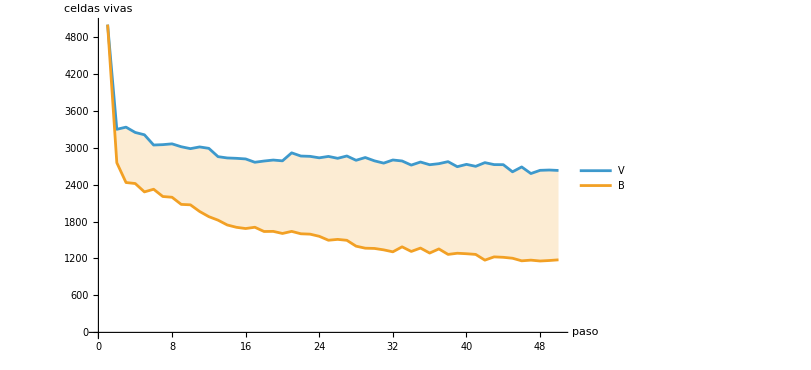

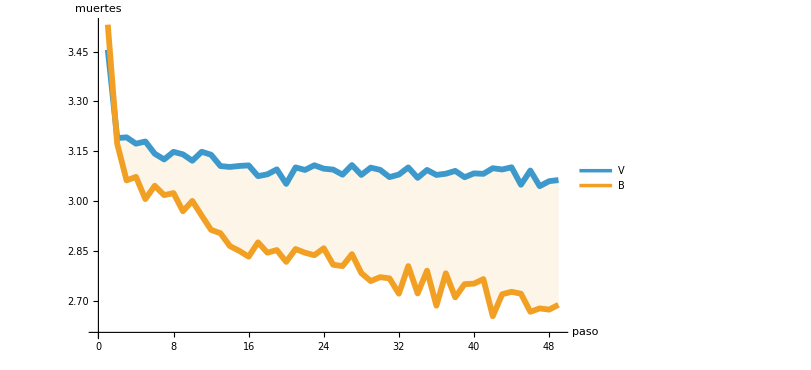
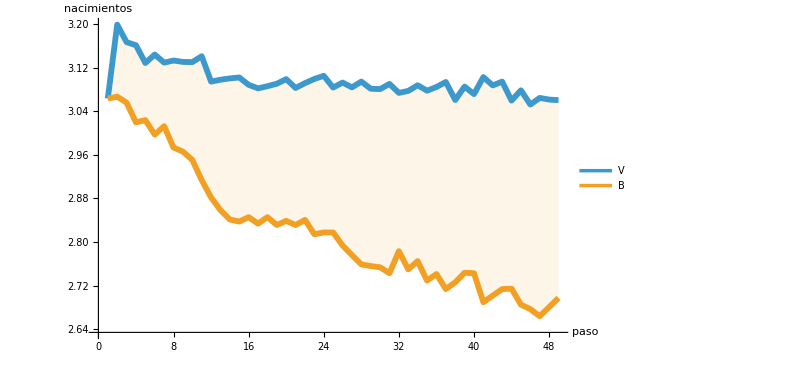
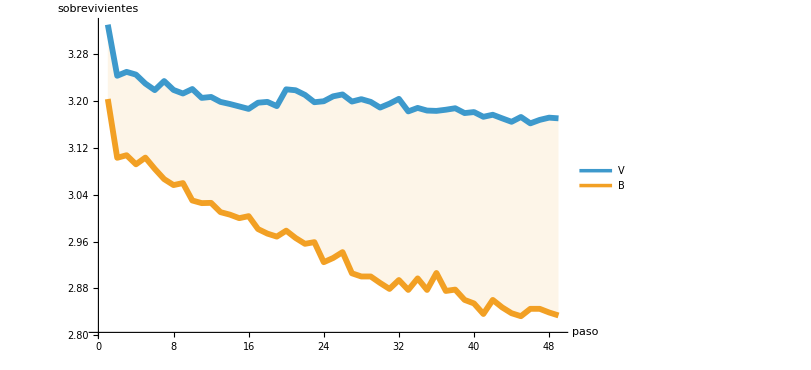

```mathematica
ListLinePlot[
countOnes[#]&/@{highlife,life},
Filling->Table[i->{1},{i,2,Length[baseC]}],
AxesLabel->{"paso","celdas vivas"},
PlotLegends->{"V","B"},
ImageSize->600]

data=metricsEvo[#]&/@{highlife,life};

dataD=data[[;;,"death"]];
dataB=data[[;;,"born"]];
dataL=data[[;;,"live"]];

dblPlots=MapThread[
ListLinePlot[
#1,
ScalingFunctions->"SignedLog",
Filling->Table[i->{1},{i,2,Length[#1]}],
FillingStyle->Directive[Opacity[.1]],
PlotStyle->{Thickness[0.007]},
ImageSize->600,
PlotLegends->{"V","B"},
AxesLabel->{"paso",#2}
]&,{{dataD,dataB,dataL},{"muertes","nacimientos","sobrevivientes"}}
]
```

## Other analysis

```mathematica
highlife=Import["./8416.mat"][[1,;;100]];
```

Import::nffil: File ./8416.mat not found during Import.

Part::partd: Part specification $Failed⟦1,1;;100⟧ is longer than depth of object.

```mathematica
contarSeguro[matriz_]:=Module[
{vecinos},
vecinos=ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},matriz,{2,2},0];
Flatten[MapThread[List,{matriz,vecinos},2],1]
]
```

```mathematica
conteosPorPaso=Counts[contarSeguro[#]]&/@highlife;
serieTemporal[par_]:=Lookup[#,Key[par],0]&/@conteosPorPaso

serie03=serieTemporal[{0,3}]; 
serie06=serieTemporal[{0,6}]; 
serie12=serieTemporal[{1,2}]; 
serie13=serieTemporal[{1,3}];
```

ListConvolve::kldims: The kernel {{1,1,1},{1,0,1},{1,1,1}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::mptd: Object $Failed at position {2, 1} in MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2] has only 0 of required 2 dimensions.

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2] is not a valid Association or a list.

ListConvolve::kldims: The kernel {{1,1,1},{1,0,1},{1,1,1}} and list 1 are not both nonempty lists with the same tensor rank.

MapThread::mptd: Object 1 at position {2, 1} in MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2] has only 0 of required 2 dimensions.

Counts::invrp: The argument MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2] is not a valid Association or a list.

ListConvolve::kldims: The kernel {{1,1,1},{1,0,1},{1,1,1}} and list 1;;100 are not both nonempty lists with the same tensor rank.

General::stop: Further output of ListConvolve::kldims will be suppressed during this calculation.

MapThread::mptd: Object 1;;100 at position {2, 1} in MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2] has only 0 of required 2 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Counts::invrp: The argument MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2] is not a valid Association or a list.

General::stop: Further output of Counts::invrp will be suppressed during this calculation.

Part::pkspec1: The expression Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,3}],0] cannot be used as a part specification.

```mathematica
paresInteres={{0,3},{0,6},{1,2},{1,3}};
total=Total[#]&/@{serie03,serie06,serie12,serie13}
N[Mean[#]]&/@{serie03,serie06,serie12,serie13}
N[#/1000000]&/@total
ListLinePlot[{serie03,serie06,serie12,serie13}]
```

{Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]],Key[{0,3}],0]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,3}],0]⟧],Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]],Key[{0,6}],0]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,6}],0]⟧],Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]],Key[{1,2}],0]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,2}],0]⟧],Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]],Key[{1,3}],0]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,3}],0]⟧]}

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0] cannot be used as a part specification.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0] cannot be used as a part specification.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

General::stop: Further output of ListConvolve::kldims will be suppressed during this calculation.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

General::stop: Further output of MapThread::intnm will be suppressed during this calculation.

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

General::stop: Further output of Counts::invrp will be suppressed during this calculation.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{Mean[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{0.,3.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,3}],0]⟧],Mean[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{0.,6.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,6}],0]⟧],Mean[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{1.,2.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,2}],0]⟧],Mean[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{1.,3.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,3}],0]⟧]}

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0] cannot be used as a part specification.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0] cannot be used as a part specification.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

General::stop: Further output of ListConvolve::kldims will be suppressed during this calculation.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

General::stop: Further output of MapThread::intnm will be suppressed during this calculation.

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

General::stop: Further output of Counts::invrp will be suppressed during this calculation.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{1.×10^-6 Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{0.,3.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,3}],0]⟧],1.×10^-6 Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{0.,6.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,6}],0]⟧],1.×10^-6 Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{1.,2.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,2}],0]⟧],1.×10^-6 Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{1.,3.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,3}],0]⟧]}

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0,1.},{1.,1.,1.}},$Failed,{2.,2.},0]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0,1.},{1.,1.,1.}},$Failed,{2.,2.},0]},2.] is not a valid Association or a list.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0,1.},{1.,1.,1.}},$Failed,{2.,2.},0]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0,1.},{1.,1.,1.}},$Failed,{2.,2.},0]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0,1.},{1.,1.,1.}},$Failed,{2.,2.},0]},2.]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

General::stop: Further output of ListConvolve::kldims will be suppressed during this calculation.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

General::stop: Further output of MapThread::intnm will be suppressed during this calculation.

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

General::stop: Further output of Counts::invrp will be suppressed during this calculation.

-Graphics-

### 4 Experiment

```mathematica
SetDirectory[NotebookDirectory[]];
base=Import["../CA/B3S23/base_50.mat"][[1]];
patternCount=ContarPatrones[base,Flatten[Table[{j,i},{i,0,8},{j,0,1}],1]];
```

```mathematica
names="C"<>ToString[#[[1]]]<>" N"<>ToString[#[[2]]]&/@Keys[patternCount];
total=Total[patternCount[[;;,1]]];
```

```mathematica
props=Values[patternCount]/total;propsSampled=Transpose[props]⟦1;;All;;4⟧;meansPct=(ToString[Slot["1"]]&)/@N[Mean/@Transpose[propsSampled] 100];legends=MapThread[#1<>": "<>#2<>"%"&,{names,meansPct}];
```

```mathematica
meansVec=N[Mean/@Transpose[propsSampled]] 100;
stdVec=N[StandardDeviation/@Transpose[propsSampled]] 100;
order=Ordering[meansVec,All,Greater];
namesSorted=names[[order]];
meansSorted=meansVec[[order]];
stdSorted=stdVec[[order]];
colors=If[StringStartsQ[#,"C0"],RGBColor[1, 0.8, 0.081],RGBColor[0.392, 1, 0.736]]&/@namesSorted;
n=Length[meansSorted];

lowerBound=MapThread[Max[#1-#2,0.001]&,{meansSorted,stdSorted}];
upperBound=meansSorted+stdSorted;

barChart=BarChart[meansSorted,ChartLabels->Placed[namesSorted,Axis,Rotate[#,90 Degree]&],ChartStyle->colors,PlotLabel->"Proporción de patrones (media ± std entre muestras)",ScalingFunctions->"Log"];

errorBars=Graphics[{Black,Thick,MapThread[Line[{{#1,Log[10,#2]},{#1,Log[10,#3]}}]&,{Range[n],lowerBound,upperBound}]}];

(*Etiquetas verticales,rotadas 90 grados,ancladas a la izquierda del punto*)
valueLabels=Graphics[{Black,MapThread[Text[ToString[NumberForm[#2,{Infinity,3}]]<>"%",{#1,Log[10,#3]+0.1},{-1,0},{0,1}  (*dirección del texto:vertical hacia arriba*)]&,{Range[n],meansSorted,upperBound}]}];

fplot=Show[barChart,errorBars,valueLabels,PlotRange->All,ImageSize->400,PlotRangeClipping->False,ImagePadding->{{20,1},{30,10}}];
Export["./../../../Documentation/img/life_pattern_count.png",fplot]
```

./../../../Documentation/img/life_pattern_count.png

### 5 Experiment

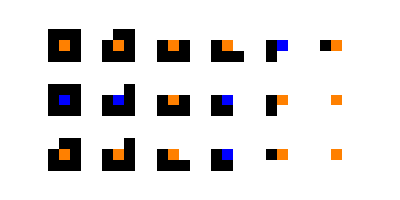

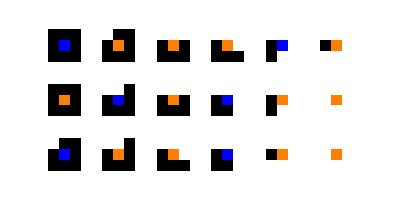

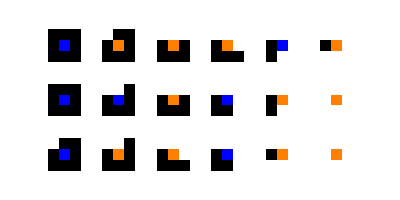

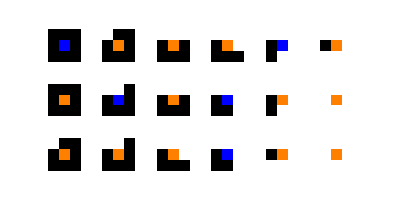

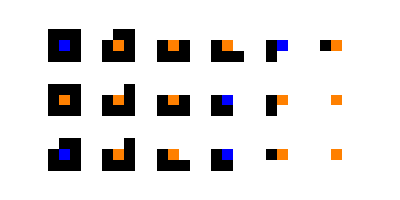

```mathematica
findRule["./life_rule_find_003.mat"]
findRule["./life_rule_find_004.mat"]
findRule["./life_rule_find_005.mat"]
findRule["./life_rule_find_01.mat"]
findRule["./life_rule_find_02.mat"]
```

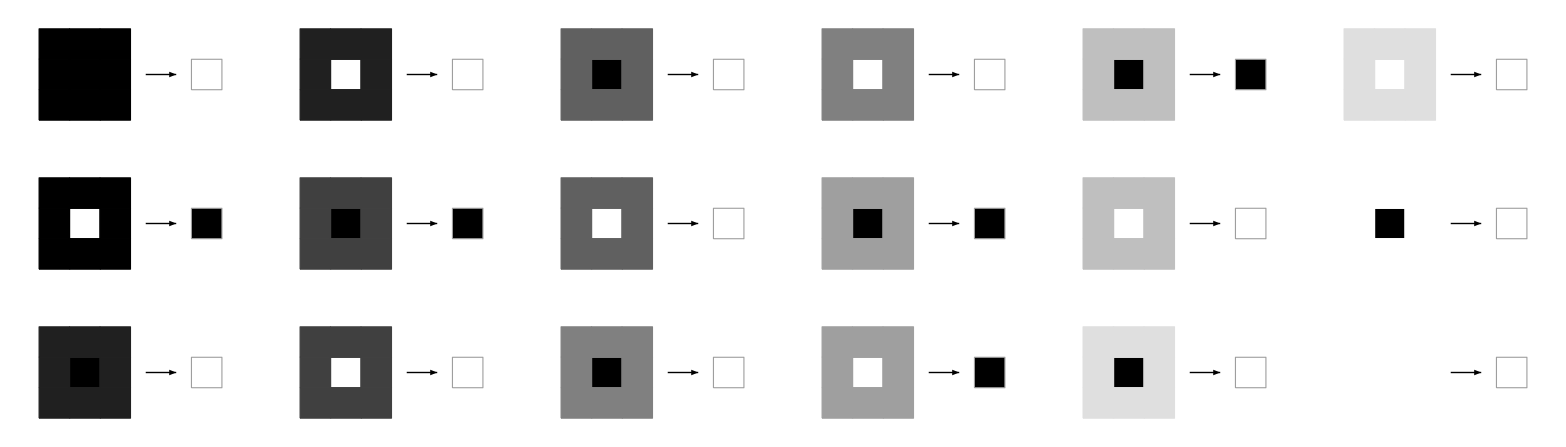

```mathematica
RulePlot[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->73952|>]]
```

```mathematica
r73952=Import["./b38_s236.mat"][[1]];
nca003=Import["./003.mat"][[1]];
r73952==nca003
patternCount[{1,8}]//Mean//N
patternCount[{1,8}]//StandardDeviation//N
total/(patternCount[{1,8}]//StandardDeviation//N)
plot5=ArrayPlot[r73952[[-1,;;30,;;30]]]
plot6=ArrayPlot[nca003[[-1,;;30,;;30]]]
```

True

1.58416

1.4647

6556.97

-Graphics-

-Graphics-

```mathematica
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/"<>"perdida_objetivo"<>".png",plot1];
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/"<>"rule_b3_s23"<>".png",plot2];
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/"<>"rule_b3_s236"<>".png",plot3];
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/"<>"b3_s236_proportion"<>".png",plot4];
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/"<>"r73952"<>".png",plot5];
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/"<>"nca003"<>".png",plot6];
```